## ANALYTIC: Data visualization pre and post by WOS

### Sorting parameters pre and postValues

```mathematica
preValues=({{α->0.13523848873130997, Dv->1011.1131394415158}, {α->0.6399462769012492, Dv->537.7607939380738}, {α->0.5027170444483849, Dv->97.10815457357153}, {α->0.0798398001852092, Dv->79.72734497440514}, {α->0.11361400734543971, Dv->1217.558830746669}, {α->0.12158899484789999, Dv->665.2336770809153}, {α->0.06000608051285142, Dv->847.0313623048015}, {α->0.18578211583236676, Dv->988.2986183380735}, {α->0.07851811305436968, Dv->800.1529415108787}, {α->0.09402255730076681, Dv->732.9978781627618}, {α->0.0780591885640549, Dv->840.2744543679529}, {α->0.1808196850455364, Dv->197.04583634347648}, {α->0.09871192170490245, Dv->223.2841132662294}, {α->0.09875310951788914, Dv->156.04385604120168}, {α->0.25784593155938984, Dv->172.56919278637528}, {α->0.529712130174677, Dv->2188.748565415073}, {α->0.05152853438650166, Dv->1037.5663239105602}, {α->0.0270071660800921, Dv->431.64258363315287}, {α->0.03447630480093485, Dv->120.44528706289503}, {α->0.12382867171576528, Dv->25.16605989943801}});
αPre=Table[α/.preValues[[i,1]],{i,1,20}];
μPre=Table[0,{i,1,20}];
DvPre=Table[Dv/.preValues[[i,2]],{i,1,20}];

postValues=({{α->0.010958529452073871, μ->0.0009682024345779599, Dv->159.64823702710353}, {α->0.469600342246159, μ->0.06802709571683775, Dv->328.6861880262081}, {α->0.0273391294684095, μ->0.004877165855163077, Dv->70.07044917129387}, {α->0.05862130178856437, μ->0.008331612935487826, Dv->122.95419350391828}, {α->0.0416935171797039, μ->0.008116067730870154, Dv->102.5515088978447}, {α->0.2555427329783495, μ->0.0510970968279005, Dv->145.1157977657312}, {α->0.17301469002403178, μ->0.024071972517164083, Dv->75.7458326559669}, {α->0.2809695268981907, μ->0.04091381390243348, Dv->436.0829063291916}, {α->0.40077050127599945, μ->0.04521252368100779, Dv->35.766509838743936}, {α->0.37514097584128925, μ->0.07448144992072454, Dv->421.44560520124014}, {α->0.034225578641521544, μ->0.004239552809997217, Dv->42.05777938521582}, {α->0.3773776218968446, μ->0.05435297091130421, Dv->193.7008187079814}, {α->0.032909759329417754, μ->0.0005119563502584925, Dv->25.523637397596275}, {α->0.16256614976481737, μ->0.022633950809094562, Dv->82.2860298248887}, {α->0.24236572063799072, μ->0.03514672512522885, Dv->418.0290743652773}, {α->0.4100669484406806, μ->0.07730900724272, Dv->1289.889957846565}, {α->0.0761841125930512, μ->0.013782787399449695, Dv->167.88189698549556}, {α->0.33165764118172714, μ->0.06537236976072648, Dv->710.5893444003543}, {α->0.04381360884181076, μ->0.006026101221396436, Dv->70.75244940219689}, {α->0.2805801421830003, μ->0.03244256902543311, Dv->35.75828233629377}});

αPost=Table[α/.postValues[[i,1]],{i,1,20}];
μPost=Table[μ/.postValues[[i,2]],{i,1,20}];
DvPost=Table[Dv/.postValues[[i,3]],{i,1,20}];
```

```mathematica
Export["mu.txt",μPost-μPre]
Export["alpha.txt",αPost-αPre]
Export["Dv.txt",DvPost-DvPre]
Export["alphamu.txt",αPost-μPost-(αPre-μPre)]
```

mu.txt

alpha.txt

Dv.txt

alphamu.txt

### α

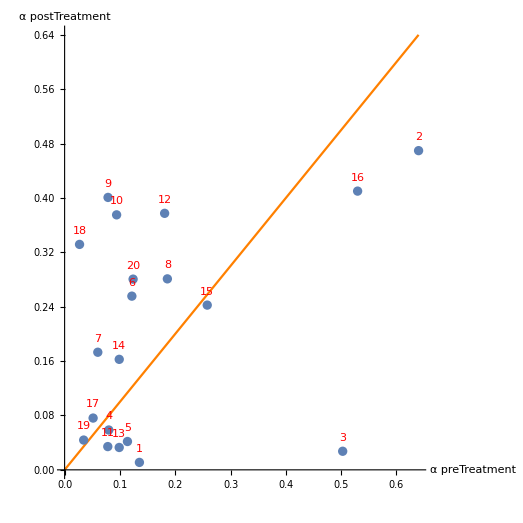

```mathematica
patientID=Range[1,20]; (*For labeling data points*)
αPrePostData=Transpose@{αPre,αPost,patientID}; 
labels=Text[#[[3]],{#[[1]],0.02+#[[2]]}]&/@αPrePostData;
Show[
Plot[α,{α,0,Max[αPre]},
PlotStyle->Orange,
PlotRange->All,
AspectRatio->1,
AxesLabel->{"α preTreatment","α postTreatment"}
],
ListPlot[αPrePostData[[All,{1,2}]]],
Graphics[{Red,labels}]
]
```

### μ

ListPlot

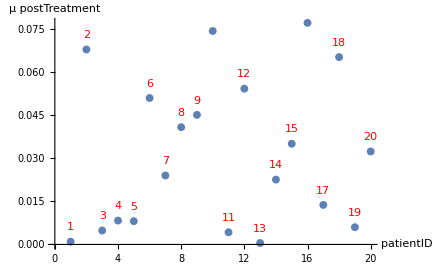

```mathematica
ListPlot
patientID=Range[1,20]; (*For labeling data points*)
μPrePostData=Transpose@{μPre,μPost,patientID}; 
labels=Text[#[[3]],{#[[3]],0.005+#[[2]]}]&/@μPrePostData;
Show[
ListPlot[μPost],
Graphics[{Red,labels}],
AxesLabel->{"patientID","μ postTreatment"}
]
```

### Dv

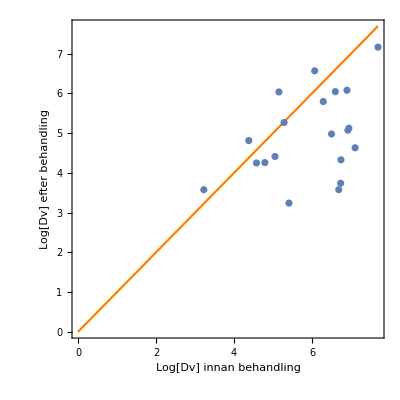

```mathematica
patientID=Range[1,20]; (*For labeling data points*)
DvPrePostData=Transpose@{Log[DvPre],Log[DvPost],patientID}; 
labels=Text[#[[3]],{#[[1]],0.1+#[[2]]}]&/@DvPrePostData;
Show[
Plot[Dv,{Dv,0,Max[Log[DvPre]]},
PlotStyle->Orange,
PlotRange->{{0,All},{0,All}},
AspectRatio->1,
(*AxesLabel->{"Log[Dv] innan behandling","Log[Dv] efter behandling"},*)
Frame->True,
FrameLabel->{Style["Log[Dv] innan behandling",FontSize->14],
Style["Log[Dv] efter behandling",FontSize->14]}

],
ListPlot[DvPrePostData[[All,{1,2}]]]
(*Graphics[{Red,labels}]*)
]
```

### α̂=α-μ

```mathematica
OverHat[α]
```

α̂

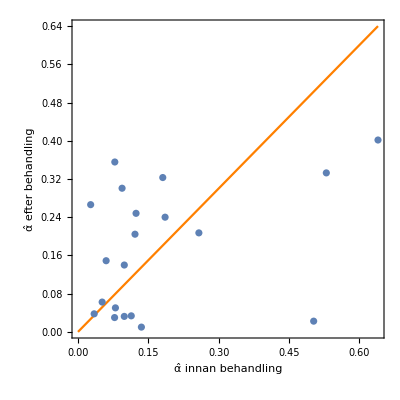

```mathematica
αμPre=αPre-μPre;
αμPost=αPost-μPost;
patientID=Range[1,20]; (*For labeling data points*)
αμPrePostData=Transpose@{αμPre,αμPost,patientID}; 
labels=Text[#[[3]],{#[[1]],0.02+#[[2]]}]&/@αμPrePostData;
Show[
Plot[αμ,{αμ,0,Max[αμPre]},
PlotStyle->Orange,
PlotRange->{{0,All},{0,All}},
AspectRatio->1,
(*AxesLabel->{"α-μ innan behandling","α-μ efter behandling"}*)
Frame->True,
FrameLabel->{Style["α̂ innan behandling",FontSize->14],
Style["α̂ efter behandling",FontSize->14]}
],
ListPlot[αμPrePostData[[All,{1,2}]]]
(*Graphics[{Red,labels}]*)
]
```

## NUMERIC: Data visualization pre and post by WOS

### Sorting parameters pre and postValues

```mathematica
preValues=({{α->0.1400, Dv->1125}, {α->0.6400, Dv->525}, {α->0.4800, Dv->125}, {α->0.0700, Dv->125}, {α->0.1100, Dv->1225}, {α->0.1200, Dv->725}, {α->0.0600, Dv->825}, {α->0.1900, Dv->1025}, {α->0.0800, Dv->825}, {α->0.0900, Dv->725}, {α->0.0800, Dv->825}, {α->0.1800, Dv->225}, {α->0.1000, Dv->225}, {α->0.0900, Dv->125}, {α->0.2500, Dv->225}, {α->0.5200, Dv->1925}, {α->0.0500, Dv->1025}, {α->0.0300, Dv->425}, {α->0.0300, Dv->125}, {α->0.1200, Dv->25}});
αPre=Table[α/.preValues[[i,1]],{i,1,20}];
μPre=Table[0,{i,1,20}];
DvPre=Table[Dv/.preValues[[i,2]],{i,1,20}];

postValues=({{α->0.0100, μ->0.0004, Dv->225}, {α->0.3400, μ->0.0136, Dv->425}, {α->0.0100, μ->0, Dv->125}, {α->0.0400, μ->0.0016, Dv->125}, {α->0.0200, μ->0.0008, Dv->225}, {α->0.0600, μ->0.0024, Dv->525}, {α->0.1100, μ->0, Dv->125}, {α->0.1800, μ->0, Dv->625}, {α->0.2900, μ->0.0116, Dv->25}, {α->0.1200, μ->0, Dv->1125}, {α->0.0200, μ->0.0008, Dv->25}, {α->0.2700, μ->0.0108, Dv->225}, {α->0.0300, μ->0, Dv->25}, {α->0.1000, μ->0, Dv->125}, {α->0.1500, μ->0, Dv->625}, {α->0.2000, μ->0.0080, Dv->1925}, {α->0.0400, μ->0, Dv->325}, {α->0.1400, μ->0.0056, Dv->1525}, {α->0.0300, μ->0, Dv->125}, {α->0.2000, μ->0.0080, Dv->25}});

αPost=Table[α/.postValues[[i,1]],{i,1,20}];
μPost=Table[μ/.postValues[[i,2]],{i,1,20}];
DvPost=Table[Dv/.postValues[[i,3]],{i,1,20}];
```

```mathematica
Export["mu.txt",μPost-μPre]
Export["alpha.txt",αPost-αPre]
Export["Dv.txt",DvPost-DvPre]
Export["alphamu.txt",αPost-μPost-(αPre-μPre)]
```

mu.txt

alpha.txt

Dv.txt

alphamu.txt

### α

```mathematica
patientID=Range[1,20]; (*For labeling data points*)
αPrePostData=Transpose@{αPre,αPost,patientID}; 
labels=Text[#[[3]],{#[[1]],0.02+#[[2]]}]&/@αPrePostData;
Show[
Plot[α,{α,0,Max[αPre]},
PlotStyle->Orange,
PlotRange->All,
AspectRatio->1,
AxesLabel->{"α preTreatment","α postTreatment"}
],
ListPlot[αPrePostData[[All,{1,2}]]],
Graphics[{Red,labels}]
]
```

-Graphics-

### μ

```mathematica
ListPlot
patientID=Range[1,20]; (*For labeling data points*)
μPrePostData=Transpose@{μPre,μPost,patientID}; 
labels=Text[#[[3]],{#[[3]],0.005+#[[2]]}]&/@μPrePostData;
Show[
ListPlot[μPost],
Graphics[{Red,labels}],
AxesLabel->{"patientID","μ postTreatment"}
]
```

ListPlot

-Graphics-

### Dv

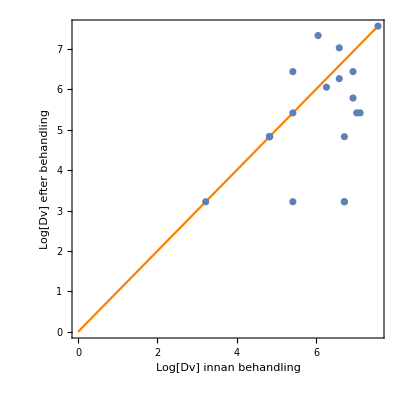

```mathematica
patientID=Range[1,20]; (*For labeling data points*)
DvPrePostData=Transpose@{Log[DvPre],Log[DvPost],patientID}; 
labels=Text[#[[3]],{#[[1]],0.1+#[[2]]}]&/@DvPrePostData;
Show[
Plot[Dv,{Dv,0,Max[Log[DvPre]]},
PlotStyle->Orange,
PlotRange->{{0,All},{0,All}},
AspectRatio->1,
(*AxesLabel->{"Log[Dv] innan behandling","Log[Dv] efter behandling"},*)
Frame->True,
FrameLabel->{Style["Log[Dv] innan behandling",FontSize->14],
Style["Log[Dv] efter behandling",FontSize->14]}

],
ListPlot[DvPrePostData[[All,{1,2}]]]
(*Graphics[{Red,labels}]*)
]
```

### α̂=α-μ

```mathematica
OverHat[α]
```

α̂

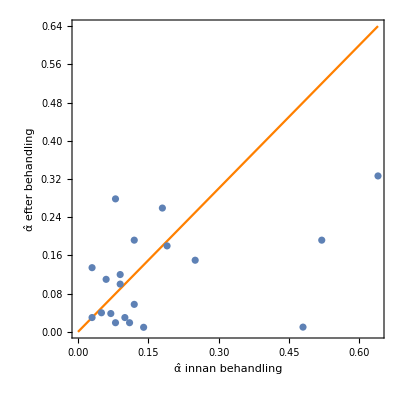

```mathematica
αμPre=αPre-μPre;
αμPost=αPost-μPost;
patientID=Range[1,20]; (*For labeling data points*)
αμPrePostData=Transpose@{αμPre,αμPost,patientID}; 
labels=Text[#[[3]],{#[[1]],0.02+#[[2]]}]&/@αμPrePostData;
Show[
Plot[αμ,{αμ,0,Max[αμPre]},
PlotStyle->Orange,
PlotRange->{{0,All},{0,All}},
AspectRatio->1,
(*AxesLabel->{"α-μ innan behandling","α-μ efter behandling"}*)
Frame->True,
FrameLabel->{Style["α̂ innan behandling",FontSize->14],
Style["α̂ efter behandling",FontSize->14]}
],
ListPlot[αμPrePostData[[All,{1,2}]]]
(*Graphics[{Red,labels}]*)
]
```